```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
results={
NotebookEvaluate[NotebookDirectory[]<>"sqrt2.nb"],
NotebookEvaluate[NotebookDirectory[]<>"sqrt22.nb"],
NotebookEvaluate[NotebookDirectory[]<>"sqrt23.nb"],
NotebookEvaluate[NotebookDirectory[]<>"phi.nb"],
NotebookEvaluate[NotebookDirectory[]<>"phi2.nb"],
NotebookEvaluate[NotebookDirectory[]<>"phi3.nb"],
NotebookEvaluate[NotebookDirectory[]<>"e.nb"],
NotebookEvaluate[NotebookDirectory[]<>"e2.nb"],
NotebookEvaluate[NotebookDirectory[]<>"e3.nb"],
NotebookEvaluate[NotebookDirectory[]<>"pi.nb"],
NotebookEvaluate[NotebookDirectory[]<>"pi2.nb"],
NotebookEvaluate[NotebookDirectory[]<>"pi3.nb"]
};
```

```mathematica
results={0.19432722586829565,0.948796383154907,5.195039007801561,{{0.696970825000789,0.13418618618195632},{1.3380017786439329,0.16313990584120797}},3.6373274654930987,{{1.3343547705985455,0.25622353320158164},{1.734718430311815,0.2010380227992543}},0.13598264046732061,0.9647626704923383,5.406740674067406,{{0.6535007731640431,0.12194622746450545},{1.3038333259695432,0.15457767946277645}},3.9543954395439544,{{1.21550418190746,0.17123441453961408},{1.6871393889811894,0.14379975077920681}},0.0970533206863487,0.9751175326468313,5.391739173917392,{{0.6583024802112771,0.1216352139064425},{1.308657190366302,0.15331575187785118}},3.992999299929993,{{1.2108451016666524,0.16118189207422784},{1.6882774839096528,0.13566872266301933}},0.19280731208058235,0.9492195142464922,5.214442888577715,{{0.6878897381855825,0.1357981551997698},{1.3291282646377294,0.16649708723159673}},3.634526905381076,{{1.3235062625071647,0.2659665894872172},{1.7268176317597228,0.20983567737821862}},0.13665179226609855,0.9645826642627503,5.3783378337833785,{{0.664568815511782,0.12381232361155248},{1.31483674920299,0.15495982890980153}},3.952795279527953,{{1.2190697775735453,0.17500584750735526},{1.6893575480237848,0.14666008366364447}},0.0966966914273309,0.9752113499730065,5.372937293729373,{{0.6591316649943406,0.12661105904029446},{1.308107221120784,0.1593585709776839}},3.9913991399139914,{{1.2027281878935858,0.1684656449935371},{1.6809869244404505,0.14261069354201972}},0.1953378476445019,0.9485148136782937,5.210642128425685,{{0.6890408450330255,0.12790809207535225},{1.33175596595567,0.15673665227001}},3.644528905781156,{{1.328176812428046,0.24349348472778298},{1.7332323436525034,0.1915761612717397}},0.14938296783862054,0.9611445088476549,5.35993599359936,{{0.6532364034591986,0.13044910110871488},{1.3005792651861696,0.1651027221317367}},3.9493949394939496,{{1.2197825234213096,0.1742012687399137},{1.6900412994346528,0.14577088226527435}},0.09659081702641088,0.9752391984499987,5.356935693569357,{{0.6729704943213272,0.12256680654973917},{1.3211986926906476,0.1524763543532619}},3.991799179917992,{{1.2210703939513654,0.15489824850562695},{1.695103058637488,0.1296237807130003}},0.19223846966953478,0.9493777726842042,5.195039007801561,{{0.69980561027814,0.13400883530271834},{1.3396496286950181,0.16290039665803535}},3.640728145629126,{{1.3330212691838037,0.2487039179229802},{1.7339883467959787,0.195354536597514}},0.14587660829474527,0.962093981703196,5.387738773877388,{{0.648612814435906,0.1257749604822851},{1.299270959488709,0.15970484600245416}},3.952595259525953,{{1.2114821282265322,0.16990392474521454},{1.684940232328676,0.14281671215293446}},0.100699510260578,0.9741572760539012,5.376737673767376,{{0.6658768050308393,0.11917143564765675},{1.3157157812227342,0.14914511718958057}},3.991799179917992,{{1.2015755036395954,0.1737532284147889},{1.6796618751852834,0.14701261962669698}}};
```

```mathematica
results=Partition[results,6]
```

{{0.194327,0.948796,5.19504,{{0.696971,0.134186},{1.338,0.16314}},3.63733,{{1.33435,0.256224},{1.73472,0.201038}}},{0.135983,0.964763,5.40674,{{0.653501,0.121946},{1.30383,0.154578}},3.9544,{{1.2155,0.171234},{1.68714,0.1438}}},{0.0970533,0.975118,5.39174,{{0.658302,0.121635},{1.30866,0.153316}},3.993,{{1.21085,0.161182},{1.68828,0.135669}}},{0.192807,0.94922,5.21444,{{0.68789,0.135798},{1.32913,0.166497}},3.63453,{{1.32351,0.265967},{1.72682,0.209836}}},{0.136652,0.964583,5.37834,{{0.664569,0.123812},{1.31484,0.15496}},3.9528,{{1.21907,0.175006},{1.68936,0.14666}}},{0.0966967,0.975211,5.37294,{{0.659132,0.126611},{1.30811,0.159359}},3.9914,{{1.20273,0.168466},{1.68099,0.142611}}},{0.195338,0.948515,5.21064,{{0.689041,0.127908},{1.33176,0.156737}},3.64453,{{1.32818,0.243493},{1.73323,0.191576}}},{0.149383,0.961145,5.35994,{{0.653236,0.130449},{1.30058,0.165103}},3.94939,{{1.21978,0.174201},{1.69004,0.145771}}},{0.0965908,0.975239,5.35694,{{0.67297,0.122567},{1.3212,0.152476}},3.9918,{{1.22107,0.154898},{1.6951,0.129624}}},{0.192238,0.949378,5.19504,{{0.699806,0.134009},{1.33965,0.1629}},3.64073,{{1.33302,0.248704},{1.73399,0.195355}}},{0.145877,0.962094,5.38774,{{0.648613,0.125775},{1.29927,0.159705}},3.9526,{{1.21148,0.169904},{1.68494,0.142817}}},{0.1007,0.974157,5.37674,{{0.665877,0.119171},{1.31572,0.149145}},3.9918,{{1.20158,0.173753},{1.67966,0.147013}}}}

```mathematica
results[[1]]
```

{0.194327,0.948796,5.19504,{{0.696971,0.134186},{1.338,0.16314}},3.63733,{{1.33435,0.256224},{1.73472,0.201038}}}

```mathematica
results=Table[Flatten[{x[[1]],x[[2]],x[[3]],ToString@x[[4,1,1]]<>" ± "<>ToString@x[[4,1,2]],ToString@x[[4,2,1]]<>" ± "<>ToString@x[[4,2,2]],x[[5]],ToString@x[[6,1,1]]<>" ± "<>ToString@x[[6,1,2]],ToString@x[[6,2,1]]<>" ± "<>ToString@x[[6,2,2]]}],{x,results}];
```

```mathematica
results={{0.19432722586829565,0.948796383154907,5.195039007801561,"0.696971 ± 0.134186","1.338 ± 0.16314",3.6373274654930987,"1.33435 ± 0.256224","1.73472 ± 0.201038"},{0.13598264046732061,0.9647626704923383,5.406740674067406,"0.653501 ± 0.121946","1.30383 ± 0.154578",3.9543954395439544,"1.2155 ± 0.171234","1.68714 ± 0.1438"},{0.0970533206863487,0.9751175326468313,5.391739173917392,"0.658302 ± 0.121635","1.30866 ± 0.153316",3.992999299929993,"1.21085 ± 0.161182","1.68828 ± 0.135669"},{0.19280731208058235,0.9492195142464922,5.214442888577715,"0.68789 ± 0.135798","1.32913 ± 0.166497",3.634526905381076,"1.32351 ± 0.265967","1.72682 ± 0.209836"},{0.13665179226609855,0.9645826642627503,5.3783378337833785,"0.664569 ± 0.123812","1.31484 ± 0.15496",3.952795279527953,"1.21907 ± 0.175006","1.68936 ± 0.14666"},{0.0966966914273309,0.9752113499730065,5.372937293729373,"0.659132 ± 0.126611","1.30811 ± 0.159359",3.9913991399139914,"1.20273 ± 0.168466","1.68099 ± 0.142611"},{0.1953378476445019,0.9485148136782937,5.210642128425685,"0.689041 ± 0.127908","1.33176 ± 0.156737",3.644528905781156,"1.32818 ± 0.243493","1.73323 ± 0.191576"},{0.14938296783862054,0.9611445088476549,5.35993599359936,"0.653236 ± 0.130449","1.30058 ± 0.165103",3.9493949394939496,"1.21978 ± 0.174201","1.69004 ± 0.145771"},{0.09659081702641088,0.9752391984499987,5.356935693569357,"0.67297 ± 0.122567","1.3212 ± 0.152476",3.991799179917992,"1.22107 ± 0.154898","1.6951 ± 0.129624"},{0.19223846966953478,0.9493777726842042,5.195039007801561,"0.699806 ± 0.134009","1.33965 ± 0.1629",3.640728145629126,"1.33302 ± 0.248704","1.73399 ± 0.195355"},{0.14587660829474527,0.962093981703196,5.387738773877388,"0.648613 ± 0.125775","1.29927 ± 0.159705",3.952595259525953,"1.21148 ± 0.169904","1.68494 ± 0.142817"},{0.100699510260578,0.9741572760539012,5.376737673767376,"0.665877 ± 0.119171","1.31572 ± 0.149145",3.991799179917992,"1.20158 ± 0.173753","1.67966 ± 0.147013"}};
```

```mathematica
Transpose[results]
```

{{0.194327,0.135983,0.0970533,0.192807,0.136652,0.0966967,0.195338,0.149383,0.0965908,0.192238,0.145877,0.1007},{0.948796,0.964763,0.975118,0.94922,0.964583,0.975211,0.948515,0.961145,0.975239,0.949378,0.962094,0.974157},{5.19504,5.40674,5.39174,5.21444,5.37834,5.37294,5.21064,5.35994,5.35694,5.19504,5.38774,5.37674},{0.696971 ± 0.134186,0.653501 ± 0.121946,0.658302 ± 0.121635,0.68789 ± 0.135798,0.664569 ± 0.123812,0.659132 ± 0.126611,0.689041 ± 0.127908,0.653236 ± 0.130449,0.67297 ± 0.122567,0.699806 ± 0.134009,0.648613 ± 0.125775,0.665877 ± 0.119171},{1.338 ± 0.16314,1.30383 ± 0.154578,1.30866 ± 0.153316,1.32913 ± 0.166497,1.31484 ± 0.15496,1.30811 ± 0.159359,1.33176 ± 0.156737,1.30058 ± 0.165103,1.3212 ± 0.152476,1.33965 ± 0.1629,1.29927 ± 0.159705,1.31572 ± 0.149145},{3.63733,3.9544,3.993,3.63453,3.9528,3.9914,3.64453,3.94939,3.9918,3.64073,3.9526,3.9918},{1.33435 ± 0.256224,1.2155 ± 0.171234,1.21085 ± 0.161182,1.32351 ± 0.265967,1.21907 ± 0.175006,1.20273 ± 0.168466,1.32818 ± 0.243493,1.21978 ± 0.174201,1.22107 ± 0.154898,1.33302 ± 0.248704,1.21148 ± 0.169904,1.20158 ± 0.173753},{1.73472 ± 0.201038,1.68714 ± 0.1438,1.68828 ± 0.135669,1.72682 ± 0.209836,1.68936 ± 0.14666,1.68099 ± 0.142611,1.73323 ± 0.191576,1.69004 ± 0.145771,1.6951 ± 0.129624,1.73399 ± 0.195355,1.68494 ± 0.142817,1.67966 ± 0.147013}}

```mathematica
t=TableForm[Transpose@results, TableHeadings->{{"sdl","H/Hmax","<k>","C","γ","<k>", "C","γ"},{"√2","√2(2)","√2(3)","ϕ","ϕ(2)","ϕ(3)","e","e(2)","e(3)","π","π(2)","π(3)"}}]
```

| √2 | √2(2) | √2(3) | ϕ | ϕ(2) | ϕ(3) | e | e(2) | e(3) | π | π(2) | π(3)
sdl | 0.194327 | 0.135983 | 0.0970533 | 0.192807 | 0.136652 | 0.0966967 | 0.195338 | 0.149383 | 0.0965908 | 0.192238 | 0.145877 | 0.1007
H/Hmax | 0.948796 | 0.964763 | 0.975118 | 0.94922 | 0.964583 | 0.975211 | 0.948515 | 0.961145 | 0.975239 | 0.949378 | 0.962094 | 0.974157
<k> | 5.19504 | 5.40674 | 5.39174 | 5.21444 | 5.37834 | 5.37294 | 5.21064 | 5.35994 | 5.35694 | 5.19504 | 5.38774 | 5.37674
C | 0.696971 ± 0.134186 | 0.653501 ± 0.121946 | 0.658302 ± 0.121635 | 0.68789 ± 0.135798 | 0.664569 ± 0.123812 | 0.659132 ± 0.126611 | 0.689041 ± 0.127908 | 0.653236 ± 0.130449 | 0.67297 ± 0.122567 | 0.699806 ± 0.134009 | 0.648613 ± 0.125775 | 0.665877 ± 0.119171
γ | 1.338 ± 0.16314 | 1.30383 ± 0.154578 | 1.30866 ± 0.153316 | 1.32913 ± 0.166497 | 1.31484 ± 0.15496 | 1.30811 ± 0.159359 | 1.33176 ± 0.156737 | 1.30058 ± 0.165103 | 1.3212 ± 0.152476 | 1.33965 ± 0.1629 | 1.29927 ± 0.159705 | 1.31572 ± 0.149145
<k> | 3.63733 | 3.9544 | 3.993 | 3.63453 | 3.9528 | 3.9914 | 3.64453 | 3.94939 | 3.9918 | 3.64073 | 3.9526 | 3.9918
C | 1.33435 ± 0.256224 | 1.2155 ± 0.171234 | 1.21085 ± 0.161182 | 1.32351 ± 0.265967 | 1.21907 ± 0.175006 | 1.20273 ± 0.168466 | 1.32818 ± 0.243493 | 1.21978 ± 0.174201 | 1.22107 ± 0.154898 | 1.33302 ± 0.248704 | 1.21148 ± 0.169904 | 1.20158 ± 0.173753
γ | 1.73472 ± 0.201038 | 1.68714 ± 0.1438 | 1.68828 ± 0.135669 | 1.72682 ± 0.209836 | 1.68936 ± 0.14666 | 1.68099 ± 0.142611 | 1.73323 ± 0.191576 | 1.69004 ± 0.145771 | 1.6951 ± 0.129624 | 1.73399 ± 0.195355 | 1.68494 ± 0.142817 | 1.67966 ± 0.147013

```mathematica
Export["digits-table.pdf",t]
```

digits-table.pdf

```mathematica
numbers=((#1)&@@@Partition[RealDigits[#,10,10^6+1][[1,2;;]],1])&/@{Sqrt[2],GoldenRatio,E,Pi};
```

```mathematica
numbers2=((#1*10+#2)&@@@Partition[RealDigits[#,10,2 10^6+1][[1,2;;]],2])&/@{Sqrt[2],GoldenRatio,E,Pi};
```

```mathematica
numbers3=((#1*100+#2*10+#3)&@@@Partition[RealDigits[#,10,3 10^6+1][[1,2;;]],3])&/@{Sqrt[2],GoldenRatio,E,Pi};
```

```mathematica
Position[numbers[[4]],2]//Length
```

1021

```mathematica
TTest/@Permutations[numbers,{2}]
```

TTest::nortst: At least one of the p-values in {0.,0.}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.,0}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.,0.}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{0.0384542,0.557823,0.253779,0.0384542,0.136062,0.349657,0.557823,0.136062,0.577515,0.253779,0.349657,0.577515}

```mathematica
TTest[numbers[[1]]]
```

TTest::nortst: At least one of the p-values in {0.}, resulting from a test for normality, is below 0.05. The tests in {T} require that the data is normally distributed.

General::munfl: 9.1393934501350227139313×10^-2726 is too small to represent as a normalized machine number; precision may be lost.

0.

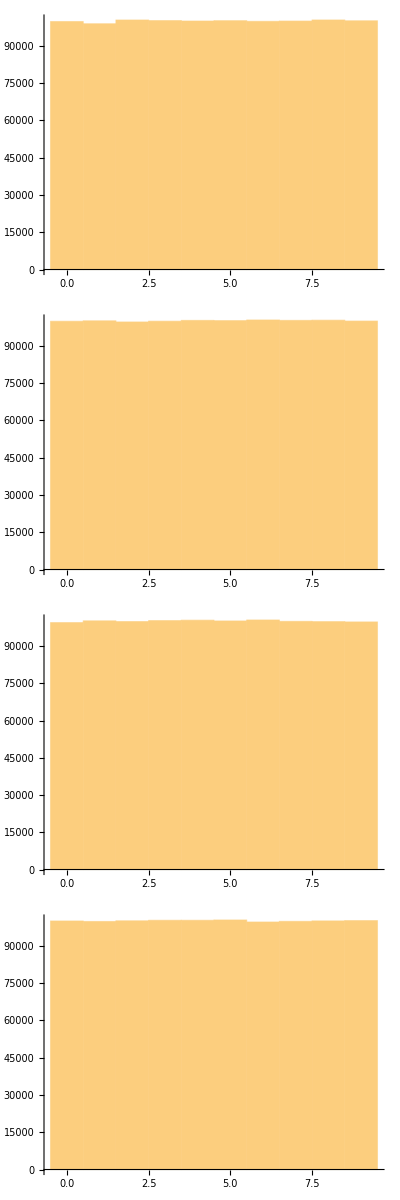

```mathematica
g=Grid[Partition[Table[Histogram[x,ImageSize->Medium],{x,numbers}],1]]
```

```mathematica
Export["million-grid.pdf", g]
```

million-grid.pdf

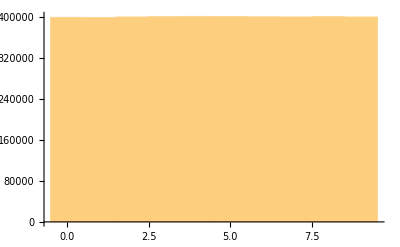

```mathematica
h=Histogram[Flatten@numbers]
```

```mathematica
Export["all-numbers-dist.pdf",h]
```

all-numbers-dist.pdf

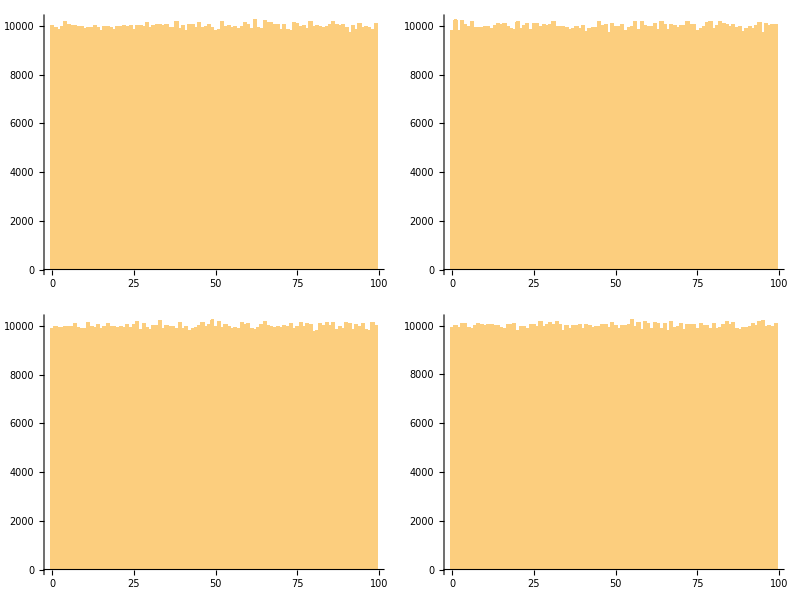

```mathematica
Grid[Partition[Table[Histogram[x,99, ImageSize->Medium],{x,numbers2}],2]]
```

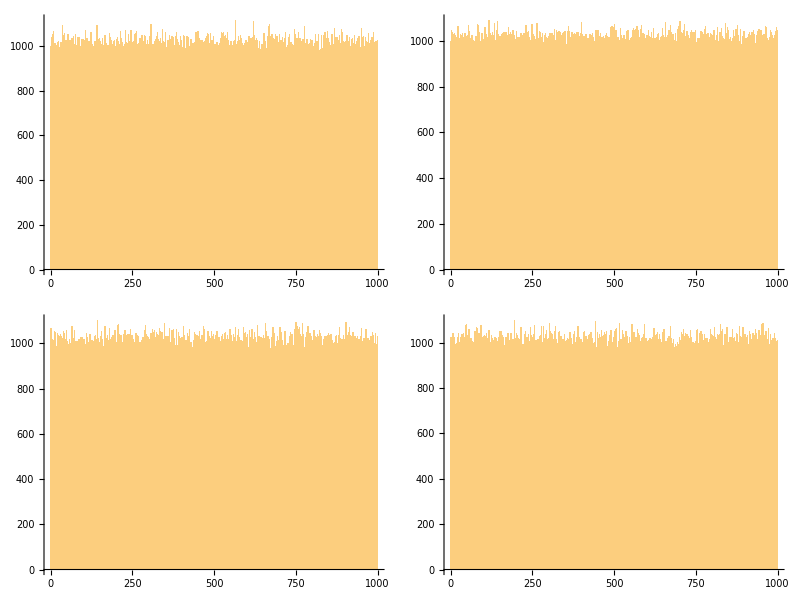

```mathematica
Grid[Partition[Table[Histogram[x,999,ImageSize->Medium],{x,numbers3}],2]]
```

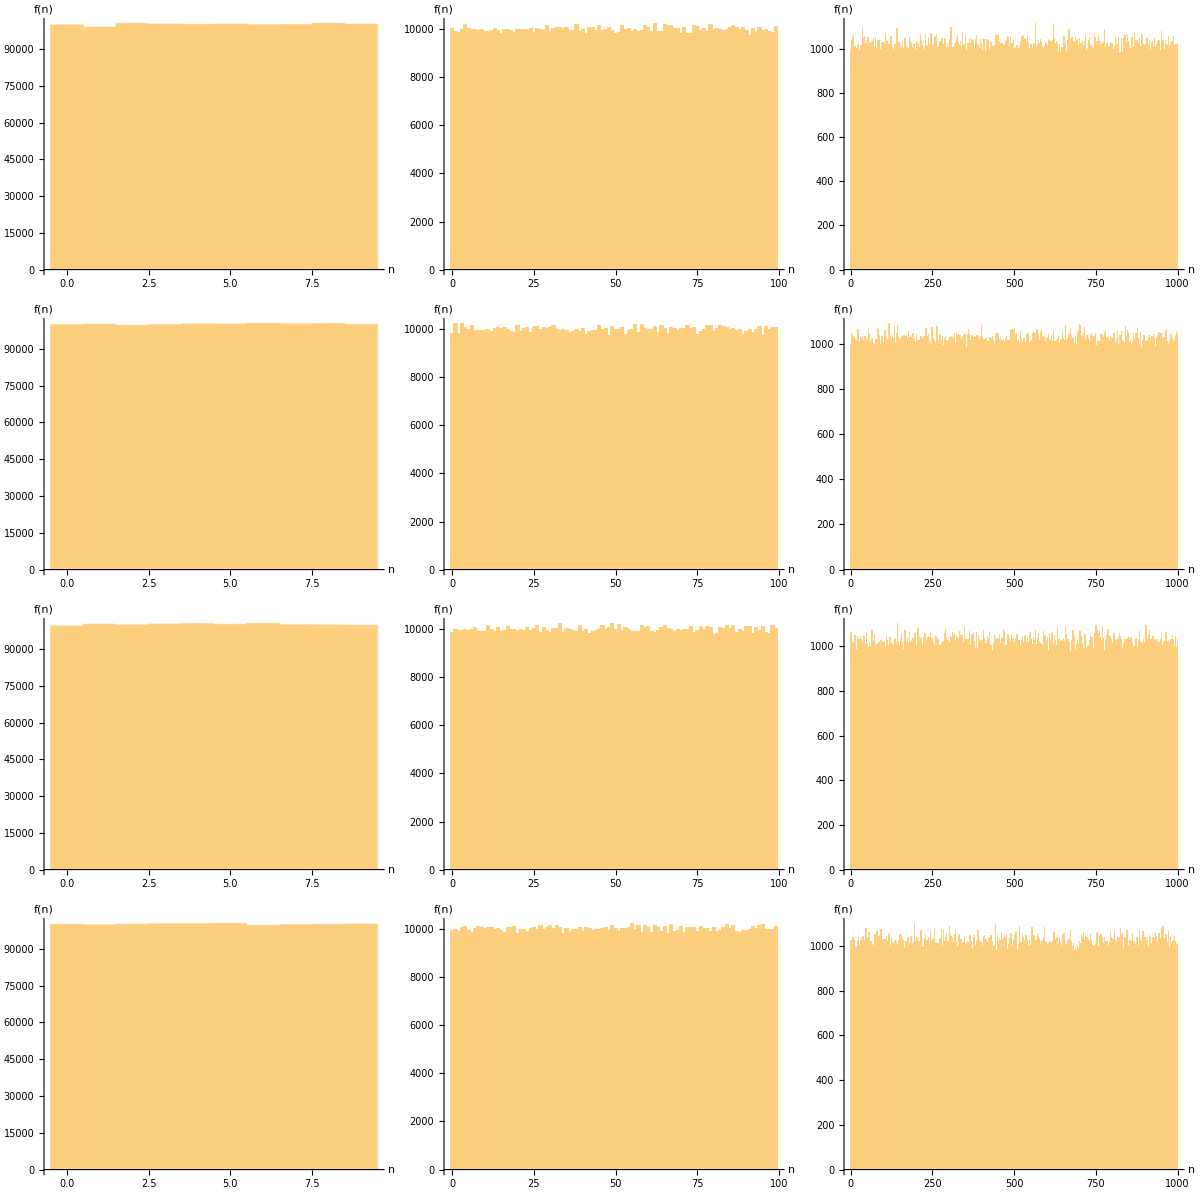

```mathematica
h=Grid[Transpose@Partition[Table[Histogram[x,999,ImageSize->Small,AxesLabel->{n,f[n]}],{x,Join[numbers,numbers2,numbers3]}],4]]
```

```mathematica
Export["numbers-dist.pdf",h]
```

numbers-dist.pdf

```mathematica
DistributionFitTest[numbers[[4]]]
```

0

```mathematica
FindDistribution/@numbers2
```

{DiscreteUniformDistribution[{0,99}],DiscreteUniformDistribution[{0,99}],DiscreteUniformDistribution[{0,99}],DiscreteUniformDistribution[{0,99}]}

```mathematica
FindDistribution/@numbers3
```

{DiscreteUniformDistribution[{0,999}],DiscreteUniformDistribution[{0,999}],DiscreteUniformDistribution[{0,999}],DiscreteUniformDistribution[{0,999}]}

```mathematica
Cases[numbers2[[1]],22]//Counts
```

<|22→97|>